```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Исходные данные

```mathematica
testNum=2;
n=20;
```

### Чтение данных из файлов

```mathematica
fileName="test"<>ToString[testNum]<>"_n"<>ToString[n]<>"_lagr.txt";
```

```mathematica
data=Import[fileName,"Table","CommentStyle"->"#"];
```

```mathematica
xVals=data[[All,1]];
yExact=data[[All,2]];
yUnif=data[[All,3]];
yCheb=data[[All,4]];
```

#### Формирование таблиц

```mathematica
pointsExact=Thread[{xVals,yExact}];
pointsUnif=Thread[{xVals,yUnif}];
pointsCheb=Thread[{xVals,yCheb}];
```

#### Построение графиков

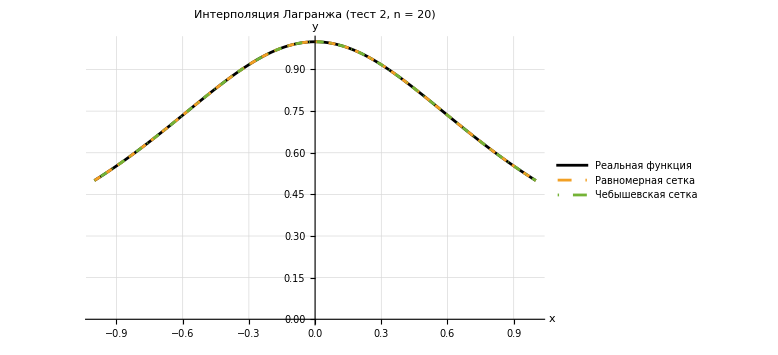

```mathematica
ListLinePlot[{pointsExact,pointsUnif,pointsCheb},PlotStyle->{Black,Dashed,DotDashed  },PlotLegends->{"Реальная функция","Равномерная сетка","Чебышевская сетка"},AxesLabel->{"x","y"},PlotLabel->Style["Интерполяция Лагранжа (тест "<>ToString[testNum]<>", n = "<>ToString[n]<>")",12,Bold],ImageSize->Large,GridLines->Automatic]
```